# EVO: Nanocosas

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]]
CreateDirectory["1.- Results"]
color = {Green, Pink}

labelFontSize = 9;
insetFontSize= 16;
```

/home/jonathan/Dropbox/Escuela/Proyecto EVOO 2018/0.- Cálculos

CreateDirectory::filex: /home/jonathan/Dropbox/Escuela/Proyecto EVOO 2018/0.- Cálculos/1.- Results already exists.

$Failed

{RGBColor[0, 1, 0],RGBColor[1, 0.5, 0.5]}

## Useful functions

### Graphing

```mathematica
legendSquare [list_,orientation_,position_]:=  (*position is a 2 elements list*)
Placed[LineLegend[list,LegendLayout-> orientation,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->5,LabelStyle->{FontSize->20, FontFamily-> "Helvetica Neue"},
LegendMarkerSize-> {30,15},
LegendMarkers->Graphics[{Thickness[0.5],Line[{{-2,0},{2,0}}]}]],position]
(*position list can be build with: Bottom, Left, Center, Right, Top, Tooltip, StatusArea or given coordinates*)
```

### Data Export/Import

```mathematica
fecha[]:=Module[{y,m,d,h,min,s}, {y,m,d,h,min,s}=Date[];
"==="<>ToString[y]<>"/"<>ToString[m]<>"/"<>ToString[d]<>"---"<>ToString[h]<>":"<>ToString[min]<>":"<>ToString[s]<>"===\n"]
```

```mathematica
importData[list_]:=Module[{i,long1={}},
For[i=1,i≤ Length[list],i++,
	If[Length[list[[i]]]==1,AppendTo[long1,i]]];
AppendTo[long1,Length[list]+1];
Table[list[[long1[[i]]+3;;long1[[i+1]]-1]],{i,1,Length[long1]-1}]]
```

### Derivatives

```mathematica
df[list_]:=Module[{xlist, ylist}, (*1st order derivative, one variable, with O(h^4) *)
xlist=list[[All,1]];
ylist = list[[All,2]];
	Table[{xlist[[i]],(1/12 ylist[[i-2]]-2/3 ylist[[i-1]]+2/3 ylist[[i+1]]-1/12 ylist[[i+2]])/(xlist[[i+1]]-xlist[[i]])},{i,3,Length[xlist]-2}]]
ddf[list_]:=Module[{xlist, ylist}, (*2st order derivative, one variable, with O(h^4) *)
xlist=list[[All,1]];
ylist = list[[All,2]];Table[{xlist[[i]],(-1/12 ylist[[i-2]]+4/3 ylist[[i-1]]-5/2 ylist[[i]]+4/3 ylist[[i+1]]-1/12 ylist[[i+2]])/(xlist[[i+1]]-xlist[[i]])^2},{i,3,Length[xlist]-2}]]
```

### Maxima/Minima Finding

```mathematica
(*Golden ration sectioning. It finds extre w/o telling if its a maxima or a minima. The analytcal expresion of the funtion is needed and it depends only in one variable
There has to be a extrema value!! Otherwise the result is one side of the interval
With this version of the code, the interval could be a Pair or a list of Pairs*)
grExtrema[func_, interval_]:=Module[{gr =  .5*(Sqrt[5.]+1) ,a,b,c,d,i,extrema = {}}, 
If[Length[Dimensions[interval]]==1,
	{a,b}= interval;
	c = b - (b-a)/gr;
	d = a + (b-a)/gr;
	While[Abs[c-d]> 1*^-8,
		 If[func[c]<func[d], b = d, a= c];
		c = b - (b-a)/gr;
		d = a + (b-a)/gr];
	extrema = .5*(a + b),
	For[i=1,i≤ Length[Dimensions[interval]],i++,
		{a,b} = interval[[i]];
		c = b - (b-a)/gr;
		d = a + (b-a)/gr;
		While[Abs[c-d]> 1*^-8,
			 If[func[c]<func[d], b = d, a= c];
			c = b - (b-a)/gr;
			d = a + (b-a)/gr];
		AppendTo[extrema,.5*(a + b)]]];
extrema]
```

```mathematica
(* A posible solution to know if there's a minima or not, is by  finding a change of sing into the given interval of the 1st derivative.  Since we are already doing this, we can determinate of the extrema it's a minimum or maxima via the 2nd derivative 
		---------NEEDS df and ddf DEFINED IN THE Derivative SECTION----------
*)
(*intExtrema[func_, interval_,h_]:= Module[{xf,dfunc,ddfunc,rootsIntMax={},rootsIntMin={},i}, 
(*interval = {a,b}, h is a number. \\ {maxs, mins}= intExtrema[f,{a,b}, h]*)
xf = Table[{x,func[x]},{x,interval[[1]],interval[[2]],h}];	
dfunc=df[xf];
ddfunc = ddf[xf];
For[i=1,i≤ Length[dfunc]-1, i++,
	If[dfunc[[i,2]]*dfunc[[i+1,2]]≤ 0, 
		If[ddfunc[[i,2]]<0,
			AppendTo[rootsIntMax,{dfunc[[i,1]],dfunc[[i+1,1]]}],  
			AppendTo[rootsIntMin,{dfunc[[i,1]],dfunc[[i+1,1]]}]]]];
{rootsIntMax,rootsIntMin}]*)
```

```mathematica
(* It's the same but it imroves the calculation of a function f(x,y)=z*)intExtrema[func_, interval_,h_]:= Module[{xf,xfS,xfP,dfuncS,ddfuncS,rootsIntMaxS={},rootsIntMinS={},dfuncP,ddfuncP,rootsIntMaxP={},rootsIntMinP={},i}, 
(*interval = {a,b}, h is a number. \\ {maxs, mins}= intExtrema[f,{a,b}, h]*)
xf = Table[Flatten[{x,func[x]}],{x,interval[[1]],interval[[2]],h}];
xfS=xf[[All,{1,2}]]; xfP = xf[[All,{1,3}]];	
dfuncS=df[xfS];dfuncP=df[xfP];
ddfuncS = ddf[xfS];ddfuncP = ddf[xfP];
For[i=1,i≤ Length[dfuncS]-1, i++,
	If[dfuncS[[i,2]]*dfuncS[[i+1,2]]≤ 0, 
		If[ddfuncS[[i,2]]<0,
			AppendTo[rootsIntMaxS,{dfuncS[[i,1]],dfuncS[[i+1,1]]}],  
			AppendTo[rootsIntMinS,{dfuncS[[i,1]],dfuncS[[i+1,1]]}]]]];
For[i=1,i≤ Length[dfuncP]-1, i++,
	If[dfuncP[[i,2]]*dfuncP[[i+1,2]]≤ 0, 
		If[ddfuncP[[i,2]]<0,
			AppendTo[rootsIntMaxP,{dfuncP[[i,1]],dfuncP[[i+1,1]]}],  
			AppendTo[rootsIntMinP,{dfuncP[[i,1]],dfuncP[[i+1,1]]}]]]];
{rootsIntMaxS,rootsIntMinS,rootsIntMaxP,rootsIntMinP}]
```

## Data of materials

```mathematica
h = 4.135668*^-15 (*eV s*);c = 3*^17 (*nm s^-1*);
FileNames["*.csv","0.- Respuestas del material"]
```

{0.- Respuestas del material/Ag_nm.csv,0.- Respuestas del material/Au_2.csv,0.- Respuestas del material/BK7.csv,0.- Respuestas del material/H2O_nm.csv}

### Drude Model for Au

```mathematica
γ = .15 (*eV*);
εDAu[ω_,ωp_]:=1 - ωp^2/(ω(ω+I γ));nDAu[ω_,ωp_]:=Sqrt[1 - ωp^2/(ω(ω+I γ))];
```

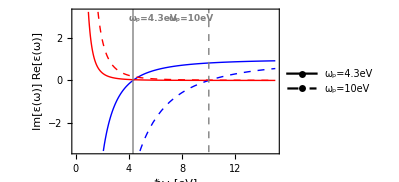

0-varepsDrude.pdf

```mathematica
Plot[{Re[εDAu[ω,4.3]],Im[εDAu[ω,4.3]],Re[εDAu[ω,10]],Im[εDAu[ω,10]]},{ω,0,15},
	PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed}}, 
	Frame-> True,FrameTicks->{{Automatic,None},{Automatic,None}}, 
	PlotLegends->Placed[LineLegend[{Black,{Black,Dashed}},{"ω_p=4.3eV","ω_p=10eV"},LegendLayout-> Automatic,
							LabelStyle->{FontSize->labelFontSize, FontFamily-> "Helvetica Neue"},LegendMarkerSize->{35,10},
							LegendMarkers->Graphics[Line[{{.5,0},{1,0}}]]],
					{Right,Top}],
	 FrameLabel->{{ Style["Re[ε(ω)]",labelFontSize,Bold,Blue]Style["Im[ε(ω)]",labelFontSize,Bold,Red],None},{Style["ℏω [eV]",labelFontSize, Bold], None}}, 
	FrameStyle-> {{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
	FrameTicksStyle->Directive[labelFontSize,Bold],
	ImageSize-> 295,
	Epilog->{Directive[{Thick,Gray}],Inset[Style["ω_p=4.3eV", labelFontSize, Bold],{4.3+1.5,2.9}],Line[{{4.3,-4},{4.3,4}}],
			Inset[Style["ω_p=10eV", labelFontSize, Bold],{10-1.3,2.9}],Directive[{Thick,Gray,Dashed}],Line[{{10,-4},{10,4}}]}]
Export["0-varepsDrude.pdf",%,ImageResolution-> 600]
```

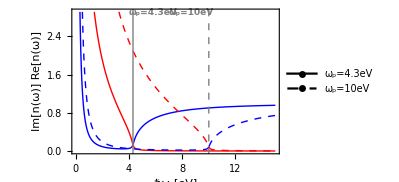

0-nDrude.pdf

```mathematica
Plot[{Re[nDAu[ω,4.3]],Im[nDAu[ω,4.3]],Re[nDAu[ω,10]],Im[nDAu[ω,10]]},{ω,0,15},
	PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed}}, 
	Frame-> True,FrameTicks->{{Automatic,None},{Automatic,None}}, 
	PlotLegends->Placed[LineLegend[{Black,{Black,Dashed}},{"ω_p=4.3eV","ω_p=10eV"},LegendLayout-> Automatic,
							LabelStyle->{FontSize->labelFontSize, FontFamily-> "Helvetica Neue"},LegendMarkerSize->{35,10},
							LegendMarkers->Graphics[Line[{{.5,0},{1,0}}]]],
					{Right,Top}],
	 FrameLabel->{{ Style["Re[n(ω)]",labelFontSize,Bold,Blue]Style["Im[n(ω)]",labelFontSize,Bold,Red],None},{Style["ℏω [eV]",labelFontSize, Bold], None}}, 
	FrameStyle-> {{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
	FrameTicksStyle->Directive[labelFontSize,Bold],
	ImageSize-> 295,
	Epilog->{Directive[{Thick,Gray}],Inset[Style["ω_p=4.3eV", labelFontSize, Bold],{4.3+1.5,2.9}],Line[{{4.3,-4},{4.3,4}}],
			Inset[Style["ω_p=10eV", labelFontSize, Bold],{10-1.3,2.9}],Directive[{Thick,Gray,Dashed}],Line[{{10,-4},{10,4}}]}]
Export["0-nDrude.pdf",%,ImageResolution-> 600]
```

### Ag: P. B. Johnson and R. W. Christy. Optical Constants of the Noble Metals, Phys. Rev. B 6, 4370-4379 (1972)

```mathematica
files=FileNames["*.csv","0.- Respuestas del material"]
nAg = Import[files[[1]],"Data"]; (* {nm, n, κ} donde N = n+iκ y ε = N^2   *) 
nAg = Drop[nAg,1];
```

{0.- Respuestas del material/Ag_nm.csv,0.- Respuestas del material/Au_2.csv,0.- Respuestas del material/BK7.csv,0.- Respuestas del material/H2O_nm.csv}

#### n=n(λ)

```mathematica
Transpose[{ nAg[[All,1]], nAg[[All,2]]+I nAg[[All,3]] }] (*N = {ω,n+iκ}) con n = Re(N), κ=Im(N) y además  N^2 = ε *)
nAgFunc = Interpolation[%]
nAgPoints = Table[{%%[[i,1]]*(1+I), %%[[i,2]]},{i,Length[%%]}];
```

{{187.9,1.07+1.212 ⅈ},{191.6,1.1+1.232 ⅈ},{195.3,1.12+1.255 ⅈ},{199.3,1.14+1.277 ⅈ},{203.3,1.15+1.296 ⅈ},{207.3,1.18+1.312 ⅈ},{211.9,1.2+1.325 ⅈ},{216.4,1.22+1.336 ⅈ},{221.4,1.25+1.342 ⅈ},{226.2,1.26+1.344 ⅈ},{231.3,1.28+1.357 ⅈ},{237.1,1.28+1.367 ⅈ},{242.6,1.3+1.378 ⅈ},{249,1.31+1.389 ⅈ},{255.1,1.33+1.393 ⅈ},{261.6,1.35+1.387 ⅈ},{268.9,1.38+1.372 ⅈ},{276.1,1.41+1.331 ⅈ},{284.4,1.41+1.264 ⅈ},{292.4,1.39+1.161 ⅈ},{300.9,1.34+0.964 ⅈ},{310.7,1.13+0.616 ⅈ},{320.4,0.81+0.392 ⅈ},{331.5,0.17+0.829 ⅈ},{342.5,0.14+1.142 ⅈ},{354.2,0.1+1.419 ⅈ},{367.9,0.07+1.657 ⅈ},{381.5,0.05+1.864 ⅈ},{397.4,0.05+2.07 ⅈ},{413.3,0.05+2.275 ⅈ},{430.5,0.04+2.462 ⅈ},{450.9,0.04+2.657 ⅈ},{471.4,0.05+2.869 ⅈ},{495.9,0.05+3.093 ⅈ},{520.9,0.05+3.324 ⅈ},{548.6,0.06+3.586 ⅈ},{582.1,0.05+3.858 ⅈ},{616.8,0.06+4.152 ⅈ},{659.5,0.05+4.483 ⅈ},{704.5,0.04+4.838 ⅈ},{756,0.03+5.242 ⅈ},{821.1,0.04+5.727 ⅈ},{892,0.04+6.312 ⅈ},{984,0.04+6.992 ⅈ},{1088,0.04+7.795 ⅈ},{1216,0.09+8.828 ⅈ},{1393,0.13+10.1 ⅈ},{1610,0.15+11.85 ⅈ},{1937,0.24+14.08 ⅈ}}

InterpolatingFunction[…]

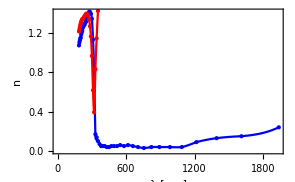

```mathematica
Show[{ListPlot[Re[nAgPoints], PlotStyle->Directive[Blue,PointSize[Large]],Frame-> True,FrameStyle-> {{Directive[Blue,Thickness[0.0035]],Directive[Red,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
 FrameLabel->{{Style["n",labelFontSize, Bold],Null},{Style["λ [nm]",labelFontSize,Bold], Null}},
 RotateLabel-> False,
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 295],
Plot[Re[nAgFunc[λ]],{λ,188,1940},PlotStyle->{Blue}, PlotRange-> All]},
ImagePadding->{{33, 33}, {33, 5}}];
Show[{ListPlot[Im[nAgPoints], PlotStyle->Directive[Red,PointSize[Large]],Frame-> True,FrameStyle-> {{Directive[Blue,Thickness[0.0035]],Directive[Red,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
 FrameLabel->{{Null,Style["κ",labelFontSize, Bold]},{Null, Null}},
 RotateLabel-> False,
FrameTicks->{{None,All},{None,None}},
FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 295],
Plot[Im[nAgFunc[λ]],{λ,188,1940},PlotStyle->{Red},Axes-> False]},
ImagePadding->{{33,33}, {33, 5}}];
Show[{%%,%}]
(*Overlay[{%,%%}]*)

(*Export["0-nAg_JC_lambda.pdf",%, ImageResolution-> 600]*)
```

#### n=n(ω)

```mathematica
Transpose[{h c/ nAg[[All,1]], nAg[[All,2]]+I nAg[[All,3]] }] (*N = {ω,n+iκ}) con n = Re(N), κ=Im(N) y además  N^2 = ε *)
nAgωFunc = Interpolation[%]
nAgωPoints = Table[{%%[[i,1]]*(1+I), %%[[i,2]]},{i,Length[%%]}];
```

{{6.60298,1.07+1.212 ⅈ},{6.47547,1.1+1.232 ⅈ},{6.35279,1.12+1.255 ⅈ},{6.22529,1.14+1.277 ⅈ},{6.10281,1.15+1.296 ⅈ},{5.98505,1.18+1.312 ⅈ},{5.85512,1.2+1.325 ⅈ},{5.73337,1.22+1.336 ⅈ},{5.60389,1.25+1.342 ⅈ},{5.48497,1.26+1.344 ⅈ},{5.36403,1.28+1.357 ⅈ},{5.23281,1.28+1.367 ⅈ},{5.11418,1.3+1.378 ⅈ},{4.98273,1.31+1.389 ⅈ},{4.86358,1.33+1.393 ⅈ},{4.74274,1.35+1.387 ⅈ},{4.61398,1.38+1.372 ⅈ},{4.49366,1.41+1.331 ⅈ},{4.36252,1.41+1.264 ⅈ},{4.24316,1.39+1.161 ⅈ},{4.1233,1.34+0.964 ⅈ},{3.99324,1.13+0.616 ⅈ},{3.87235,0.81+0.392 ⅈ},{3.74269,0.17+0.829 ⅈ},{3.62248,0.14+1.142 ⅈ},{3.50282,0.1+1.419 ⅈ},{3.37238,0.07+1.657 ⅈ},{3.25216,0.05+1.864 ⅈ},{3.12204,0.05+2.07 ⅈ},{3.00194,0.05+2.275 ⅈ},{2.882,0.04+2.462 ⅈ},{2.75161,0.04+2.657 ⅈ},{2.63195,0.05+2.869 ⅈ},{2.50192,0.05+3.093 ⅈ},{2.38184,0.05+3.324 ⅈ},{2.26158,0.06+3.586 ⅈ},{2.13142,0.05+3.858 ⅈ},{2.01151,0.06+4.152 ⅈ},{1.88127,0.05+4.483 ⅈ},{1.76111,0.04+4.838 ⅈ},{1.64114,0.03+5.242 ⅈ},{1.51102,0.04+5.727 ⅈ},{1.39092,0.04+6.312 ⅈ},{1.26087,0.04+6.992 ⅈ},{1.14035,0.04+7.795 ⅈ},{1.02031,0.09+8.828 ⅈ},{0.890668,0.13+10.1 ⅈ},{0.770621,0.15+11.85 ⅈ},{0.640527,0.24+14.08 ⅈ}}

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.600123} lies outside the range of data in the interpolating function. Extrapolation will be used.

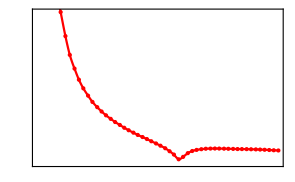
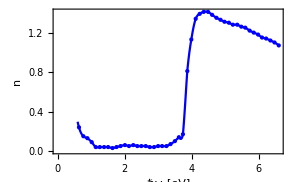

```mathematica
Show[{ListPlot[Re[nAgωPoints], PlotStyle->Directive[Blue,PointSize[Large]],Frame-> True,FrameStyle-> {{Directive[Blue,Thickness[0.0035]],Directive[Red,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
 FrameLabel->{{Style["n",labelFontSize, Bold],Null},{Style["ℏω [eV]",labelFontSize,Bold], Style["λ [nm]",labelFontSize,Bold]}},
 RotateLabel-> False,
FrameTicks->{{Automatic,None},{Automatic,Table[{h c / nAg[[i,1]],nAg[[i,1]]},{i,1,Length[nAg],8}]}},
FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 295],
Plot[Re[nAgωFunc[ω]],{ω,.6,6.6},PlotStyle->{Blue}, PlotRange-> All]},
ImagePadding->{{33, 33}, {33, 33}}];
Show[{ListPlot[Im[nAgωPoints], PlotStyle->Directive[Red,PointSize[Large]],Frame-> True,FrameStyle-> {{Directive[Blue,Thickness[0.0035]],Directive[Red,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
 FrameLabel->{{Null,Style["κ",labelFontSize, Bold]},{Null, Null}},
 RotateLabel-> False,
FrameTicks->{{None,All},{None,None}},
FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 295],
Plot[Im[nAgωFunc[ω]],{ω,.6,6.6},PlotStyle->{Red},Axes-> False]},
ImagePadding->{{33,33}, {33, 33}}];

Overlay[{%,%%}]
(*Export["0-nAg_JC_omega.pdf",%, ImageResolution-> 600]*)
```

InterpolatingFunction::dmval: Input value {0.600123} lies outside the range of data in the interpolating function. Extrapolation will be used.

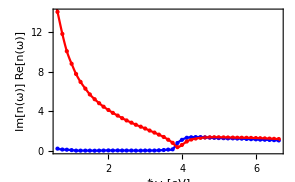

```mathematica
Show[{ListPlot[{Re[nAgωPoints],Im[nAgωPoints]}, PlotStyle->{Directive[Blue,PointSize[Large]],Directive[Red,PointSize[Large]]},Frame-> True,PlotRange->All,FrameStyle-> Directive[Black,Thickness[0.0035]],
 FrameLabel->{{ Style["Re[n(ω)]",labelFontSize,Bold,Blue] Style["Im[n(ω)]",labelFontSize,Bold,Red],None},{Style["ℏω [eV]",labelFontSize, Bold], Style["λ [nm]",labelFontSize, Bold]}}, 
 RotateLabel-> True,
FrameTicks->{{Automatic,None},{Automatic,Table[{h c / nAg[[i,1]],nAg[[i,1]]},{i,1,Length[nAg],8}]}},
FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 295],
Plot[{Re[nAgωFunc[ω]],Im[nAgωFunc[ω]]},{ω,.6,6.6},PlotStyle->{Blue,Red}, PlotRange-> All]},
ImagePadding->{{33, 33}, {33, 33}}]
```

### Au: Johnson, P. B.; Christy, R. W. (1972). “Optical Constants of the Noble Metals”. Physical Review B. 6 (12): 4370–4379

```mathematica
files=FileNames["*.csv","0.- Respuestas del material"]
nAueV = Import[files[[2]],"Data"] ;(*1 es Ag, 2 es Au, 3 es en H2O en nm y 4 es en μm*) (* {nm, n, κ} donde N = n+iκ y ε = N^2   *) 
nAueV  = Drop[Drop[nAueV,-4],2]
```

{0.- Respuestas del material/Ag_nm.csv,0.- Respuestas del material/Au_2.csv,0.- Respuestas del material/BK7.csv,0.- Respuestas del material/H2O_nm.csv}

{{0.64,0.92,13.78},{0.77,0.56,11.21},{0.89,0.43,9.519},{1.02,0.35,8.145},{1.14,0.27,7.15},{1.26,0.22,6.35},{1.39,0.17,5.663},{1.51,0.16,5.083},{1.64,0.14,4.542},{1.76,0.13,4.103},{1.88,0.14,3.697},{2.01,0.21,3.272},{2.13,0.29,2.863},{2.26,0.43,2.455},{2.38,0.62,2.081},{2.5,1.04,1.833},{2.63,1.31,1.849},{2.75,1.38,1.914},{2.88,1.45,1.948},{3.,1.46,1.958},{3.12,1.47,1.952},{3.25,1.46,1.933},{3.37,1.48,1.895},{3.5,1.5,1.866},{3.62,1.48,1.871},{3.74,1.48,1.883},{3.87,1.54,1.898},{3.99,1.53,1.893},{4.12,1.53,1.889},{4.24,1.49,1.878},{4.36,1.47,1.869},{4.49,1.43,1.847},{4.61,1.38,1.803},{4.74,1.35,1.749},{4.86,1.33,1.688},{4.98,1.33,1.631},{5.11,1.32,1.577},{5.23,1.32,1.536},{5.36,1.3,1.497},{5.48,1.31,1.46},{5.6,1.3,1.427},{5.73,1.3,1.387},{5.85,1.3,1.35},{5.98,1.3,1.304},{6.1,1.33,1.277},{6.22,1.33,1.251},{6.35,1.34,1.226},{6.47,1.32,1.203},{6.6,1.28,1.188}}

#### n=n(λ)

```mathematica
Transpose[{ h c /nAueV[[All,1]], nAueV[[All,2]]+I nAueV[[All,3]] }] (*N = {ω,n+iκ}) con n = Re(N), κ=Im(N) y además  N^2 = ε *)
nAuFunc = Interpolation[%]
nAuPoints = Table[{%%[[i,1]]*(1+I), %%[[i,2]]},{i,Length[%%]}];
```

{{1938.59,0.92+13.78 ⅈ},{1611.3,0.56+11.21 ⅈ},{1394.05,0.43+9.519 ⅈ},{1216.37,0.35+8.145 ⅈ},{1088.33,0.27+7.15 ⅈ},{984.683,0.22+6.35 ⅈ},{892.59,0.17+5.663 ⅈ},{821.656,0.16+5.083 ⅈ},{756.525,0.14+4.542 ⅈ},{704.943,0.13+4.103 ⅈ},{659.947,0.14+3.697 ⅈ},{617.264,0.21+3.272 ⅈ},{582.488,0.29+2.863 ⅈ},{548.982,0.43+2.455 ⅈ},{521.303,0.62+2.081 ⅈ},{496.28,1.04+1.833 ⅈ},{471.749,1.31+1.849 ⅈ},{451.164,1.38+1.914 ⅈ},{430.799,1.45+1.948 ⅈ},{413.567,1.46+1.958 ⅈ},{397.66,1.47+1.952 ⅈ},{381.754,1.46+1.933 ⅈ},{368.16,1.48+1.895 ⅈ},{354.486,1.5+1.866 ⅈ},{342.735,1.48+1.871 ⅈ},{331.738,1.48+1.883 ⅈ},{320.594,1.54+1.898 ⅈ},{310.952,1.53+1.893 ⅈ},{301.141,1.53+1.889 ⅈ},{292.618,1.49+1.878 ⅈ},{284.564,1.47+1.869 ⅈ},{276.325,1.43+1.847 ⅈ},{269.132,1.38+1.803 ⅈ},{261.751,1.35+1.749 ⅈ},{255.288,1.33+1.688 ⅈ},{249.137,1.33+1.631 ⅈ},{242.799,1.32+1.577 ⅈ},{237.228,1.32+1.536 ⅈ},{231.474,1.3+1.497 ⅈ},{226.405,1.31+1.46 ⅈ},{221.554,1.3+1.427 ⅈ},{216.527,1.3+1.387 ⅈ},{212.086,1.3+1.35 ⅈ},{207.475,1.3+1.304 ⅈ},{203.394,1.33+1.277 ⅈ},{199.47,1.33+1.251 ⅈ},{195.386,1.34+1.226 ⅈ},{191.762,1.32+1.203 ⅈ},{187.985,1.28+1.188 ⅈ}}

InterpolatingFunction[…]

```mathematica
Transpose[{ h c/nAueV[[All,1]], nAueV[[All,2]]+I nAueV[[All,3]]}] (*N = {ω,n+iκ}) con n = Re(N), κ=Im(N) y además  N^2 = ε *)
nAuFunc = Interpolation[%]
nAuPoints = Transpose[{ (1+I)%%[[All,1]], %%[[All,2]] }] (*N = {ω,n+iκ}) con n = Re(N), κ=Im(N) y además  N^2 = ε *)
```

{{1938.59,0.92+13.78 ⅈ},{1611.3,0.56+11.21 ⅈ},{1394.05,0.43+9.519 ⅈ},{1216.37,0.35+8.145 ⅈ},{1088.33,0.27+7.15 ⅈ},{984.683,0.22+6.35 ⅈ},{892.59,0.17+5.663 ⅈ},{821.656,0.16+5.083 ⅈ},{756.525,0.14+4.542 ⅈ},{704.943,0.13+4.103 ⅈ},{659.947,0.14+3.697 ⅈ},{617.264,0.21+3.272 ⅈ},{582.488,0.29+2.863 ⅈ},{548.982,0.43+2.455 ⅈ},{521.303,0.62+2.081 ⅈ},{496.28,1.04+1.833 ⅈ},{471.749,1.31+1.849 ⅈ},{451.164,1.38+1.914 ⅈ},{430.799,1.45+1.948 ⅈ},{413.567,1.46+1.958 ⅈ},{397.66,1.47+1.952 ⅈ},{381.754,1.46+1.933 ⅈ},{368.16,1.48+1.895 ⅈ},{354.486,1.5+1.866 ⅈ},{342.735,1.48+1.871 ⅈ},{331.738,1.48+1.883 ⅈ},{320.594,1.54+1.898 ⅈ},{310.952,1.53+1.893 ⅈ},{301.141,1.53+1.889 ⅈ},{292.618,1.49+1.878 ⅈ},{284.564,1.47+1.869 ⅈ},{276.325,1.43+1.847 ⅈ},{269.132,1.38+1.803 ⅈ},{261.751,1.35+1.749 ⅈ},{255.288,1.33+1.688 ⅈ},{249.137,1.33+1.631 ⅈ},{242.799,1.32+1.577 ⅈ},{237.228,1.32+1.536 ⅈ},{231.474,1.3+1.497 ⅈ},{226.405,1.31+1.46 ⅈ},{221.554,1.3+1.427 ⅈ},{216.527,1.3+1.387 ⅈ},{212.086,1.3+1.35 ⅈ},{207.475,1.3+1.304 ⅈ},{203.394,1.33+1.277 ⅈ},{199.47,1.33+1.251 ⅈ},{195.386,1.34+1.226 ⅈ},{191.762,1.32+1.203 ⅈ},{187.985,1.28+1.188 ⅈ}}

InterpolatingFunction[…]

{{1938.59+1938.59 ⅈ,0.92+13.78 ⅈ},{1611.3+1611.3 ⅈ,0.56+11.21 ⅈ},{1394.05+1394.05 ⅈ,0.43+9.519 ⅈ},{1216.37+1216.37 ⅈ,0.35+8.145 ⅈ},{1088.33+1088.33 ⅈ,0.27+7.15 ⅈ},{984.683+984.683 ⅈ,0.22+6.35 ⅈ},{892.59+892.59 ⅈ,0.17+5.663 ⅈ},{821.656+821.656 ⅈ,0.16+5.083 ⅈ},{756.525+756.525 ⅈ,0.14+4.542 ⅈ},{704.943+704.943 ⅈ,0.13+4.103 ⅈ},{659.947+659.947 ⅈ,0.14+3.697 ⅈ},{617.264+617.264 ⅈ,0.21+3.272 ⅈ},{582.488+582.488 ⅈ,0.29+2.863 ⅈ},{548.982+548.982 ⅈ,0.43+2.455 ⅈ},{521.303+521.303 ⅈ,0.62+2.081 ⅈ},{496.28+496.28 ⅈ,1.04+1.833 ⅈ},{471.749+471.749 ⅈ,1.31+1.849 ⅈ},{451.164+451.164 ⅈ,1.38+1.914 ⅈ},{430.799+430.799 ⅈ,1.45+1.948 ⅈ},{413.567+413.567 ⅈ,1.46+1.958 ⅈ},{397.66+397.66 ⅈ,1.47+1.952 ⅈ},{381.754+381.754 ⅈ,1.46+1.933 ⅈ},{368.16+368.16 ⅈ,1.48+1.895 ⅈ},{354.486+354.486 ⅈ,1.5+1.866 ⅈ},{342.735+342.735 ⅈ,1.48+1.871 ⅈ},{331.738+331.738 ⅈ,1.48+1.883 ⅈ},{320.594+320.594 ⅈ,1.54+1.898 ⅈ},{310.952+310.952 ⅈ,1.53+1.893 ⅈ},{301.141+301.141 ⅈ,1.53+1.889 ⅈ},{292.618+292.618 ⅈ,1.49+1.878 ⅈ},{284.564+284.564 ⅈ,1.47+1.869 ⅈ},{276.325+276.325 ⅈ,1.43+1.847 ⅈ},{269.132+269.132 ⅈ,1.38+1.803 ⅈ},{261.751+261.751 ⅈ,1.35+1.749 ⅈ},{255.288+255.288 ⅈ,1.33+1.688 ⅈ},{249.137+249.137 ⅈ,1.33+1.631 ⅈ},{242.799+242.799 ⅈ,1.32+1.577 ⅈ},{237.228+237.228 ⅈ,1.32+1.536 ⅈ},{231.474+231.474 ⅈ,1.3+1.497 ⅈ},{226.405+226.405 ⅈ,1.31+1.46 ⅈ},{221.554+221.554 ⅈ,1.3+1.427 ⅈ},{216.527+216.527 ⅈ,1.3+1.387 ⅈ},{212.086+212.086 ⅈ,1.3+1.35 ⅈ},{207.475+207.475 ⅈ,1.3+1.304 ⅈ},{203.394+203.394 ⅈ,1.33+1.277 ⅈ},{199.47+199.47 ⅈ,1.33+1.251 ⅈ},{195.386+195.386 ⅈ,1.34+1.226 ⅈ},{191.762+191.762 ⅈ,1.32+1.203 ⅈ},{187.985+187.985 ⅈ,1.28+1.188 ⅈ}}

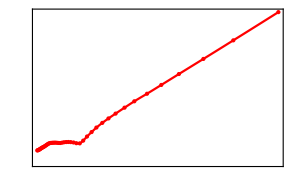
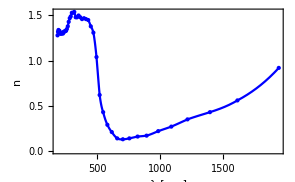

```mathematica
Show[{ListPlot[Re[nAuPoints], PlotStyle->Directive[Blue,PointSize[Large]],Frame-> True,PlotRange->All,FrameStyle-> {{Directive[Blue,Thickness[0.0035]],Directive[Red,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
 FrameLabel->{{Style["n",labelFontSize, Bold],Null},{Style["λ [nm]",labelFontSize,Bold], Null}},
 RotateLabel-> False,
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 295],
Plot[Re[nAuFunc[λ]],{λ,188,1940},PlotStyle->{Blue}, PlotRange-> All]},
ImagePadding->{{33, 33}, {33, 5}}];
Show[{ListPlot[Im[nAuPoints], PlotStyle->Directive[Red,PointSize[Large]],Frame-> True,PlotRange->All,FrameStyle-> {{Directive[Blue,Thickness[0.0035]],Directive[Red,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
 FrameLabel->{{Null,Style["κ",labelFontSize, Bold]},{Null, Null}},
 RotateLabel-> False,
FrameTicks->{{None,All},{None,None}},
FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 295],
Plot[Im[nAuFunc[λ]],{λ,188,1940},PlotStyle->{Red},Axes-> False,PlotRange->All]},
ImagePadding->{{33,33}, {33, 5}}];

Overlay[{%,%%}]
(*Export["0-nAu_JC_lambda.pdf",%, ImageResolution-> 600]*)
```

#### n=n(ω)

```mathematica
Transpose[{ nAueV[[All,1]], nAueV[[All,2]]+I nAueV[[All,3]] }] (*N = {ω,n+iκ}) con n = Re(N), κ=Im(N) y además  N^2 = ε *)
nAuωFunc = Interpolation[%]
nAuωPoints = Table[{%%[[i,1]]*(1+I), %%[[i,2]]},{i,Length[%%]}];
```

{{0.64,0.92+13.78 ⅈ},{0.77,0.56+11.21 ⅈ},{0.89,0.43+9.519 ⅈ},{1.02,0.35+8.145 ⅈ},{1.14,0.27+7.15 ⅈ},{1.26,0.22+6.35 ⅈ},{1.39,0.17+5.663 ⅈ},{1.51,0.16+5.083 ⅈ},{1.64,0.14+4.542 ⅈ},{1.76,0.13+4.103 ⅈ},{1.88,0.14+3.697 ⅈ},{2.01,0.21+3.272 ⅈ},{2.13,0.29+2.863 ⅈ},{2.26,0.43+2.455 ⅈ},{2.38,0.62+2.081 ⅈ},{2.5,1.04+1.833 ⅈ},{2.63,1.31+1.849 ⅈ},{2.75,1.38+1.914 ⅈ},{2.88,1.45+1.948 ⅈ},{3.,1.46+1.958 ⅈ},{3.12,1.47+1.952 ⅈ},{3.25,1.46+1.933 ⅈ},{3.37,1.48+1.895 ⅈ},{3.5,1.5+1.866 ⅈ},{3.62,1.48+1.871 ⅈ},{3.74,1.48+1.883 ⅈ},{3.87,1.54+1.898 ⅈ},{3.99,1.53+1.893 ⅈ},{4.12,1.53+1.889 ⅈ},{4.24,1.49+1.878 ⅈ},{4.36,1.47+1.869 ⅈ},{4.49,1.43+1.847 ⅈ},{4.61,1.38+1.803 ⅈ},{4.74,1.35+1.749 ⅈ},{4.86,1.33+1.688 ⅈ},{4.98,1.33+1.631 ⅈ},{5.11,1.32+1.577 ⅈ},{5.23,1.32+1.536 ⅈ},{5.36,1.3+1.497 ⅈ},{5.48,1.31+1.46 ⅈ},{5.6,1.3+1.427 ⅈ},{5.73,1.3+1.387 ⅈ},{5.85,1.3+1.35 ⅈ},{5.98,1.3+1.304 ⅈ},{6.1,1.33+1.277 ⅈ},{6.22,1.33+1.251 ⅈ},{6.35,1.34+1.226 ⅈ},{6.47,1.32+1.203 ⅈ},{6.6,1.28+1.188 ⅈ}}

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.600123} lies outside the range of data in the interpolating function. Extrapolation will be used.

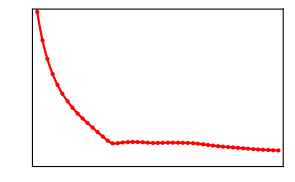
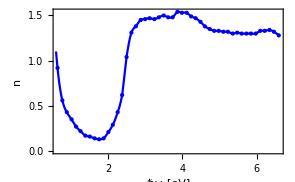

```mathematica
Show[{ListPlot[Re[nAuωPoints], PlotStyle->Directive[Blue,PointSize[Large]],Frame-> True,PlotRange->All,FrameStyle-> {{Directive[Blue,Thickness[0.0035]],Directive[Red,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
 FrameLabel->{{Style["n",labelFontSize, Bold],Null},{Style["ℏω [eV]",labelFontSize,Bold], Style["λ [nm]",labelFontSize,Bold]}},
 RotateLabel-> False,
FrameTicks->{{Automatic,None},{Automatic,Table[{h c / nAg[[i,1]],nAg[[i,1]]},{i,1,Length[nAg],8}]}},
FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 295],
Plot[Re[nAuωFunc[ω]],{ω,.6,6.6},PlotStyle->{Blue}, PlotRange-> All]},
ImagePadding->{{33, 33}, {33, 33}}];
Show[{ListPlot[Im[nAuωPoints], PlotStyle->Directive[Red,PointSize[Large]],Frame-> True,PlotRange->All,FrameStyle-> {{Directive[Blue,Thickness[0.0035]],Directive[Red,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
 FrameLabel->{{Null,Style["κ",labelFontSize, Bold]},{Null, Null}},
 RotateLabel-> False,
FrameTicks->{{None,All},{None,None}},
FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 295],
Plot[Im[nAuωFunc[ω]],{ω,.6,6.6},PlotRange-> All,PlotStyle->{Red},Axes-> False]},
ImagePadding->{{33,33}, {33, 33}}];

Overlay[{%,%%}]
(*Export["0-nAu_JC_omega.pdf",%, ImageResolution-> 600]*)
```

InterpolatingFunction::dmval: Input value {0.600123} lies outside the range of data in the interpolating function. Extrapolation will be used.

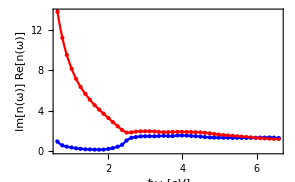

```mathematica
Show[{ListPlot[{Re[nAuωPoints],Im[nAuωPoints]}, PlotStyle->{Directive[Blue,PointSize[Large]],Directive[Red,PointSize[Large]]},Frame-> True,PlotRange->All,FrameStyle-> Directive[Black,Thickness[0.0035]],
 FrameLabel->{{ Style["Re[n(ω)]",labelFontSize,Bold,Blue]Style["Im[n(ω)]",labelFontSize,Bold,Red],None},{Style["ℏω [eV]",labelFontSize, Bold], Style["λ [nm]",labelFontSize, Bold]}}, 
 RotateLabel-> True,
FrameTicks->{{Automatic,None},{Automatic,Table[{h c / nAg[[i,1]],nAg[[i,1]]},{i,1,Length[nAg],8}]}},
FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 295],
Plot[{Re[nAuωFunc[ω]],Im[nAuωFunc[ω]]},{ω,.6,6.6},PlotStyle->{Blue,Red}, PlotRange-> All]},
ImagePadding->{{33, 33}, {33, 33}}]
```

## Mie Theroy: Coefficients, π_n&τ_n, Q_sca & Q_ext

### Coefficients (a_n & b_n) (needed)

http://functions.wolfram.com/Bessel-TypeFunctions/SphericalBesselJ/20/ShowAll.html
						 d/dz f_n(z) = f_(n-1)(z) - (n+1)/z f_n(z)
 						d/dz g_n(z)  = f_n(z) +z d/dz f_n(z)
							 = f_n(z) +  z (f_(n-1)(z) - (n+1)/z f_n(z))
							=  f_n(z) +  z f_(n-1)(z) - (n+1)f_n(z)
							=  z f_(n-1)(z) +(1+- n-1)f_n(z)
							= z f_(n-1)(z) - n f_n(z)

```mathematica
rbψ[n_,z_] := z *SphericalBesselJ[n,z]
rbξ[n_,z_] := z *SphericalHankelH1[n,z]
drbψ[n_,z_]:=-n *SphericalBesselJ[n,z]+ z * SphericalBesselJ[n-1,z]  
drbξ[n_,z_]:=-n * SphericalHankelH1[n,z] + z* SphericalHankelH1[n-1,z]
```

```mathematica
mieCoef[n_,x_,m_]:= Module[{an,bn},  (*n=orden, x=size parameter, m = Subscript[n, part]/Subscript[n, medium]; si n es una lista -> {{Subscript[a, 1], Subscript[a, 2],...,Subscript[a, n]},{Subscript[b, 1], Subscript[b, 2],...,Subscript[b, n]}}, si no, sólo da la pareja*)
an = (m rbψ[n, m x]drbψ[n, x] - rbψ[n,x]drbψ[n,m x])/(m rbψ[n,m x]drbξ[n, x]-rbξ[n, x]drbψ[n, m x]);
bn = (rbψ[n, m x]drbψ[n, x] -m rbψ[n,x]drbψ[n,m x])/(rbψ[n,m x]drbξ[n, x]-m rbξ[n, x]drbψ[n, m x]);
{an,bn}]
```

### π_n & τ_n

```mathematica
pi[n_,θ_]:=Module[{f}, f[0]=0;f[1]=1;   f[i_]:=f[i]=(2 i -1)/(i-1)Cos[θ]f[i-1]-i/(i-1)f[i-2];f[n]]
tau[n_,θ_]:=Module[{f}, f[0]=0; f[1]=1; f[i_]:=f[i]=(2 i -1)/(i-1)Cos[θ]f[i-1]-i/(i-1)f[i-2]; n Cos[θ] f[n] - (n+1)f[n-1]]
```

### Q_sca & Q_ext

```mathematica
scaQn[indexes_,λ_,rad_]:= Module[{an,bn,sum, nmax,x,m},
x = 2* π *indexes[[1]] *rad / λ;
m = indexes[[2]]/indexes[[1]];   (*Partícula / medio*)
nmax =  Round[x+4 x^(1/3)+2];
{an,bn} = mieCoef[Table[i,{i,nmax}],x,m];
sum = Sum[(2*i+1)* (Abs[an[[i]] ]^2+Abs[bn[[i]] ]^2),{i, Length[an]}];
sum = ((λ^2 )* sum)/(2*π*( Abs[indexes[[1]]]^2));
sum = sum / (π  *(rad^2))]
```

```mathematica
extQn[indexes_,λ_,rad_]:= Module[{sum,an,bn,nmax,x,m},
x = 2* π *indexes[[1]] *rad / λ;
m = indexes[[2]]/indexes[[1]];   (*Partícula / medio*)
nmax =  Round[x+4 x^(1/3)+2];
{an,bn} = mieCoef[Table[i,{i,nmax}],x,m];
sum = Sum[(2*i+1)* Re[ an[[i]] + bn[[i]]  ],{i, Length[an]}];
sum = ((λ^2 )* sum)/(2*π*( Abs[indexes[[1]]]^2));
sum = sum / (π  *(rad^2))]
```

```mathematica
scaextQn[indexes_,λ_,rad_]:= Module[{sumExt, sumSca,an,bn,nmax,x,m},
x = 2* π *indexes[[1]] *rad / λ;
m = indexes[[2]]/indexes[[1]];   (*Partícula / medio*)
nmax =  Round[x+4 x^(1/3)+2];
{an,bn} = mieCoef[Table[i,{i,nmax}],x,m];
sumExt = Sum[(2*i+1)* Re[ an[[i]] + bn[[i]]  ],{i, Length[an]}];sumExt = ((λ^2 )* sumExt)/(2*π*( Abs[indexes[[1]]]^2));
sumSca = Sum[(2*i+1)* (Abs[an[[i]] ]^2+Abs[bn[[i]] ]^2),{i, Length[an]}];sumSca = ((λ^2 )* sumSca)/(2*π*( Abs[indexes[[1]]]^2));
{sumExt,sumSca}  / (π  *(rad^2))]
```

```mathematica
scaextQn[{1.,nAuFunc[500]},500,radio]
```

Table::iterb: Iterator {i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

{1/radio^2 12665.1 (3 Re[(-0.0248559-0.0233379 ⅈ) radio SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio] ((0.0122895+0.0233379 ⅈ) radio SphericalBesselJ[-1+Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio]-SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio] Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}])-(0.0190344-0.0689854 ⅈ) radio SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio] (0.0125664 radio SphericalBesselJ[-1+Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio]-SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio] Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}])]+5 Re[1/(-0.0125664 radio SphericalHankelH1[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio] ((0.0122895+0.0233379 ⅈ) radio SphericalBesselJ[-1+Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio]-SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio] Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}])-(0.0313239-0.0456475 ⅈ) radio SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio] (0.0125664 radio SphericalHankelH1[-1+Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio]-SphericalHankelH1[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio] Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}]))+1/((-0.0122895-0.0233379 ⅈ) radio SphericalHankelH1[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio] ((0.0122895+0.0233379 ⅈ) radio SphericalBesselJ[-1+Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio]-SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio] Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}])+(0.0122895+0.0233379 ⅈ) radio SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio] (0.0125664 radio SphericalHankelH1[-1+Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio]-SphericalHankelH1[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio] Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}]))]),1/radio^2 12665.1 (3 (Abs[-0.0125664 radio SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio] ((0.0122895+0.0233379 ⅈ) radio SphericalBesselJ[-1+Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio]-SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio] Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}])-(0.0313239-0.0456475 ⅈ) radio SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio] (0.0125664 radio SphericalBesselJ[-1+Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio]-SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio] Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}])]^2+Abs[(-0.0122895-0.0233379 ⅈ) radio SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio] ((0.0122895+0.0233379 ⅈ) radio SphericalBesselJ[-1+Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio]-SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio] Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}])+(0.0122895+0.0233379 ⅈ) radio SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio] (0.0125664 radio SphericalBesselJ[-1+Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio]-SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio] Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}])]^2)+5 (1/Abs[-0.0125664 radio SphericalHankelH1[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio] ((0.0122895+0.0233379 ⅈ) radio SphericalBesselJ[-1+Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio]-SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio] Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}])-(0.0313239-0.0456475 ⅈ) radio SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio] (0.0125664 radio SphericalHankelH1[-1+Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio]-SphericalHankelH1[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio] Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}])]^2+1/Abs[(-0.0122895-0.0233379 ⅈ) radio SphericalHankelH1[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio] ((0.0122895+0.0233379 ⅈ) radio SphericalBesselJ[-1+Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio]-SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio] Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}])+(0.0122895+0.0233379 ⅈ) radio SphericalBesselJ[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],(0.0122895+0.0233379 ⅈ) radio] (0.0125664 radio SphericalHankelH1[-1+Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio]-SphericalHankelH1[Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}],0.0125664 radio] Table[i,{i,Round[2+0.929958 radio^(1/3)+0.0125664 radio]}])]^2))}

# Spheres

## Mie Theory

```mathematica
dir = "3.- TMie";
 CreateDirectory[dir];
```

CreateDirectory::filex: /home/jonathan/Dropbox/Escuela/Proyecto EVOO 2018/0.- Cálculos/3.- TMie already exists.

```mathematica
radio=9(*nm*)
```

9

```mathematica
file = OpenAppend[FileNameJoin[{dir,"AuNP_"<>ToString[radio]<>"nm_JC_Cext.csv"}], BinaryFormat->True];
WriteString[file,"lambda (nm), E(eV), Cext [nm^2], Csca [nm^2]\n"];
Table[Flatten[{λ,h c/(λ),π (radio^2) *scaextQn[{1.33,nAuFunc[λ]},λ,radio]}],{λ,250.,1880.}];
Export[file, %];
Close[FileNameJoin[{dir,"AuNP_"<>ToString[radio]<>"nm_JC_Cext.csv"}]];
```

### a = 9nm

```mathematica
FileNames["*csv",dir]
dataAu = Import[%[[4]],"Data"];
dataAg = Import[%%[[2]],"Data"];
```

{3.- TMie/AgNP_1000nm_JC_Cext.csv,3.- TMie/AgNP_15nm_JC_Cext.csv,3.- TMie/AuNP_1000nm_JC_Cext.csv,3.- TMie/AuNP_15nm_JC_Cext.csv,3.- TMie/AuNP_9nm_JC_Cext.csv}

```mathematica
radio = 9;
```

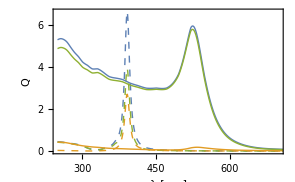

TMie_r_9nm.pdf

```mathematica
ListLinePlot[{Transpose[{dataAu[[All,1]],dataAu[[All,3]]/(π *(radio^2))}],Transpose[{dataAu[[All,1]],dataAu[[All,4]]/(π *(radio^2))}],
		Transpose[{dataAu[[All,1]],(dataAu[[All,3]]-dataAu[[All,4]])/(π *(radio^2))}]}, 
	PlotStyle->Thick, PlotRange->{{Automatic,700},{Automatic,All}},
	PlotLegends->Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"Q_ext","Q_sca","Q_abs"},LegendLayout-> "Column",
							LabelStyle->{FontSize->labelFontSize, FontFamily-> "Helvetica Neue"},LegendMarkerSize->{20,5},
							LegendMarkers->Graphics[Line[{{.5,0},{1,0}}]]],
					{Right,Top}],
	Frame-> True,FrameTicks->{{Automatic,None},{Automatic,None}}, 
	 FrameLabel->{{ Style["Q]",labelFontSize,Bold],None},{Style["λ [nm]",labelFontSize, Bold], None}}, 
	FrameStyle-> {{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
	FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 295];

ListLinePlot[{Transpose[{dataAg[[All,1]],dataAg[[All,3]]/(10 π *(radio^2))}],Transpose[{dataAg[[All,1]],dataAg[[All,4]]/(10 π *(radio^2))}],
		Transpose[{dataAg[[All,1]],(dataAg[[All,3]]-dataAg[[All,4]])/(10 π *(radio^2))}]}, 
	PlotStyle->Table[{Dashed,Thick},{i,3}], PlotRange->{{Automatic,700},{Automatic,All}},
	PlotLegends->Placed[LineLegend[{Thick,{Dashed, Thick}},{"Au","Ag × 0.1"},LegendLayout-> "Column",
							LabelStyle->{FontSize->labelFontSize, FontFamily-> "Helvetica Neue"},LegendMarkerSize->{20,5},
							LegendMarkers->Graphics[Line[{{.5,0},{1,0}}]]],
					{Right,Top}],
	Frame-> True,FrameTicks->{{Automatic,None},{Automatic,None}}, 
	 FrameLabel->{{ Style["Q",labelFontSize,Bold],None},{Style["λ [nm]",labelFontSize, Bold], None}}, 
	FrameStyle-> {{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
	FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 295];
Show[{%,%%}]

Export["TMie_r_9nm.pdf",%,ImageResolution-> 600]
```

### a = 15nm

```mathematica
FileNames["*csv",dir]
dataAu = Import[%[[4]],"Data"];
dataAg = Import[%%[[2]],"Data"];
```

{3.- TMie\AgNP_1000nm_JC_Cext.csv,3.- TMie\AgNP_15nm_JC_Cext.csv,3.- TMie\AuNP_1000nm_JC_Cext.csv,3.- TMie\AuNP_15nm_JC_Cext.csv}

```mathematica
radio = 15;
```

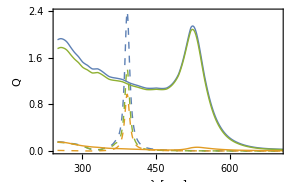

TMie_r_15nm.pdf

```mathematica
ListLinePlot[{Transpose[{dataAu[[All,1]],dataAu[[All,3]]/(π *(radio^2))}],Transpose[{dataAu[[All,1]],dataAu[[All,4]]/(π *(radio^2))}],
		Transpose[{dataAu[[All,1]],(dataAu[[All,3]]-dataAu[[All,4]])/(π *(radio^2))}]}, 
	PlotStyle->Thick, PlotRange->{{Automatic,700},{Automatic,All}},
	PlotLegends->Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"Q_ext","Q_sca","Q_abs"},LegendLayout-> "Column",
							LabelStyle->{FontSize->labelFontSize, FontFamily-> "Helvetica Neue"},LegendMarkerSize->{20,5},
							LegendMarkers->Graphics[Line[{{.5,0},{1,0}}]]],
					{Right,Top}],
	Frame-> True,FrameTicks->{{Automatic,None},{Automatic,None}}, 
	 FrameLabel->{{ Style["Q]",labelFontSize,Bold],None},{Style["λ [nm]",labelFontSize, Bold], None}}, 
	FrameStyle-> {{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
	FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 295];

ListLinePlot[{Transpose[{dataAg[[All,1]],dataAg[[All,3]]/(10 π *(radio^2))}],Transpose[{dataAg[[All,1]],dataAg[[All,4]]/(10 π *(radio^2))}],
		Transpose[{dataAg[[All,1]],(dataAg[[All,3]]-dataAg[[All,4]])/(10 π *(radio^2))}]}, 
	PlotStyle->Table[{Dashed,Thick},{i,3}], PlotRange->{{Automatic,700},{Automatic,All}},
	PlotLegends->Placed[LineLegend[{Thick,{Dashed, Thick}},{"Au","Ag × 0.1"},LegendLayout-> "Column",
							LabelStyle->{FontSize->labelFontSize, FontFamily-> "Helvetica Neue"},LegendMarkerSize->{20,5},
							LegendMarkers->Graphics[Line[{{.5,0},{1,0}}]]],
					{Right,Top}],
	Frame-> True,FrameTicks->{{Automatic,None},{Automatic,None}}, 
	 FrameLabel->{{ Style["Q",labelFontSize,Bold],None},{Style["λ [nm]",labelFontSize, Bold], None}}, 
	FrameStyle-> {{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
	FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 295];
Show[{%,%%}]

Export["TMie_r_15nm.pdf",%,ImageResolution-> 600]
```

### a = 1μm

```mathematica
FileNames["*csv",dir]
dataAu = Import[%[[3]],"Data"];
dataAg = Import[%%[[1]],"Data"];
```

{3.- TMie\AgNP_1000nm_JC_Cext.csv,3.- TMie\AgNP_15nm_JC_Cext.csv,3.- TMie\AuNP_1000nm_JC_Cext.csv,3.- TMie\AuNP_15nm_JC_Cext.csv}

```mathematica
radio = 1*^3;
```

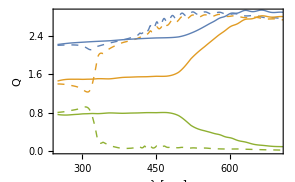

TMie_r_1000nm.pdf

```mathematica
ListLinePlot[{Transpose[{dataAu[[All,1]],dataAu[[All,3]]/(π *(radio^2))}],Transpose[{dataAu[[All,1]],dataAu[[All,4]]/(π *(radio^2))}],
		Transpose[{dataAu[[All,1]],(dataAu[[All,3]]-dataAu[[All,4]])/(π *(radio^2))}]}, 
	PlotStyle->Thick, PlotRange->{{Automatic,700},{Automatic,All}},
	PlotLegends->Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"Q_ext","Q_sca","Q_abs"},LegendLayout-> "Column",
							LabelStyle->{FontSize->labelFontSize, FontFamily-> "Helvetica Neue"},LegendMarkerSize->{20,5},
							LegendMarkers->Graphics[Line[{{.5,0},{1,0}}]]],
					{Right,Center}],
	Frame-> True,FrameTicks->{{Automatic,None},{Automatic,None}}, 
	 FrameLabel->{{ Style["Q]",labelFontSize,Bold],None},{Style["λ [nm]",labelFontSize, Bold], None}}, 
	FrameStyle-> {{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
	FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 295];

ListLinePlot[{Transpose[{dataAg[[All,1]],dataAg[[All,3]]/( π *(radio^2))}],Transpose[{dataAg[[All,1]],dataAg[[All,4]]/( π *(radio^2))}],
		Transpose[{dataAg[[All,1]],(dataAg[[All,3]]-dataAg[[All,4]])/( π *(radio^2))}]}, 
	PlotStyle->Table[{Dashed,Thick},{i,3}], PlotRange->{{Automatic,700},{Automatic,All}},
	PlotLegends->Placed[LineLegend[{Thick,{Dashed, Thick}},{"Au","Ag"},LegendLayout-> "Column",
							LabelStyle->{FontSize->labelFontSize, FontFamily-> "Helvetica Neue"},LegendMarkerSize->{20,5},
							LegendMarkers->Graphics[Line[{{.5,0},{1,0}}]]],
					{Right,Center}],
	Frame-> True,FrameTicks->{{Automatic,None},{Automatic,None}}, 
	 FrameLabel->{{ Style["Q",labelFontSize,Bold],None},{Style["λ [nm]",labelFontSize, Bold], None}}, 
	FrameStyle-> {{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
	FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 295];
Show[{%,%%}]
Export["TMie_r_1000nm.pdf",%,ImageResolution-> 600]
```

## Experimental data

```mathematica
FileNames["*.txt","2.- Mediciones"]
dataA = Import[%[[#]],"Data"]&/@Table[i,{i,1,Length[%],2}];
dataT = Import[%%[[#]],"Data"]&/@Table[i,{i,2,Length[%%],2}];

dataA = Table[Select[Drop[dataA[[i]],1],360<#[[1]]<800&],{i,Length[dataA]}];
dataT = Table[Select[Drop[dataT[[i]],1],360<#[[1]]<800&],{i,Length[dataT]}];
```

{2.- Mediciones\1.- AuJ_A.txt,2.- Mediciones\1.- AuJ_T.txt,2.- Mediciones\2.- AgJ_A.txt,2.- Mediciones\2.- AgJ_T.txt,2.- Mediciones\3.- AgC_A.txt,2.- Mediciones\3.- AgC_T.txt,2.- Mediciones\4.- AgJH2011_A.txt,2.- Mediciones\4.- AgJH2011_T.txt,2.- Mediciones\5.- AgJAuJ11_A.txt,2.- Mediciones\5.- AgJAuJ11_T.txt,2.- Mediciones\6.- AgCAuJ11_A.txt,2.- Mediciones\6.- AgCAuJ11_T.txt,2.- Mediciones\7.- AgCAuJ21_A.txt,2.- Mediciones\7.- AgCAuJ21_T.txt,2.- Mediciones\8.- AgJAuJ41_A.txt,2.- Mediciones\8.- AgJAuJ41_T.txt,2.- Mediciones\9.- AgCAuJ41_A.txt,2.- Mediciones\9.- AgCAuJ41_T.txt}

```mathematica
mLabel = {"Au^J","Ag^J","Ag^C","Ag^J-H_20 @ 1:1","Ag^J-Au^J @ 1:1","Ag^C-Au^J @ 1:1","Ag^C-Au^J @ 2:1", "Ag^J-Au^J @ 4:1","Ag^C-Au^J @ 4:1"}
```

{Au^J,Ag^J,Ag^C,Ag^J-H_20 @ 1:1,Ag^J-Au^J @ 1:1,Ag^C-Au^J @ 1:1,Ag^C-Au^J @ 2:1,Ag^J-Au^J @ 4:1,Ag^C-Au^J @ 4:1}

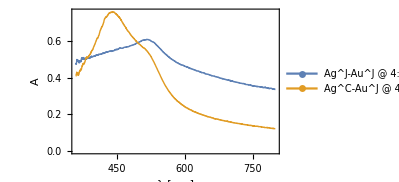

AbsNp_3.pdf

```mathematica
ListLinePlot[dataA[[#]]&/@Table[i,{i,8,9}], 
	PlotStyle->Table[{Thick,ColorData[97,i]},{i,2}], PlotRange->Automatic,
PlotLegends->Placed[LineLegend[Table[ColorData[97,i],{i,2}],mLabel[[8;;9]],LegendLayout-> "Column",
							LabelStyle->{FontSize->labelFontSize, FontFamily-> "Helvetica Neue"},LegendMarkerSize->{20,5},
							LegendMarkers->Graphics[Line[{{.5,0},{1,0}}]]],
					{Right,Top}],
	Frame-> True,FrameTicks->{{Automatic,None},{Automatic,None}}, 
	 FrameLabel->{{ Style["A",labelFontSize,Bold],None},{Style["λ [nm]",labelFontSize, Bold], None}}, 
	FrameStyle-> {{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
	FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 295]
Export["AbsNp_3.pdf",%,ImageResolution-> 600]
```

```mathematica
rAu = 15/2; rAg= 40/2; long = 4*^6 (*nm*);
```

```mathematica
dataTAuAg=dataT[[#]]&/@{1,3};
dataAAuAg=dataA[[#]]&/@{1,3};
radios = {rAu, rAg};
```

```mathematica
cExtAu = Table[{λ,extQn[{1.33,nAuFunc[λ]},λ,rAu]},{λ,dataTAuAg[[1,All,1]]}];
cExtAg = Table[{λ,extQn[{1.33,nAgFunc[λ]},λ,rAg]},{λ,dataTAuAg[[2,All,1]]}];
cExtAuAg= {%%,%};
```

```mathematica
frac = Table[{dataTAuAg[[i,j,1]], (-Log[dataTAuAg[[i,j,2]]/100])/(cExtAuAg[[i,j,2]]* long / (4π (radios[[i]])^3/3)) },{i,Length[dataTAuAg]},{j,Length[dataTAuAg[[i]]]}];
```

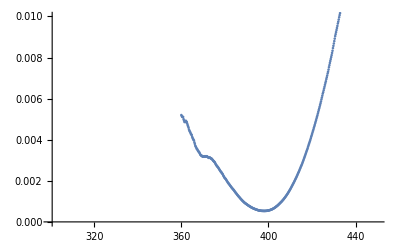

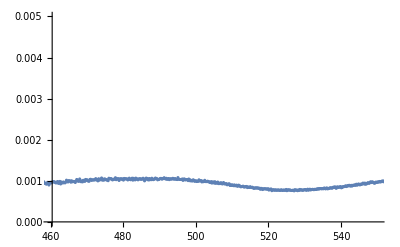

```mathematica
ListPlot[frac[[2]],PlotRange->{{300,450},{0,.01}}]
ListPlot[frac[[1]],PlotRange->{{460,550},{0,.005}}]
```

```mathematica
Select[frac[[1]],460<#[[1]]<540&][[All,2]]//Max
Select[frac[[2]],380<#[[1]]<410&][[All,2]]//Max
```

0.00107868

0.00212339

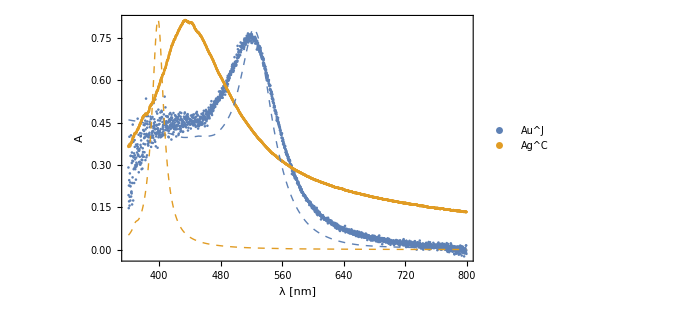

AuAg.pdf

```mathematica
f={.0008,.00075};
Show[{ListPlot[dataAAuAg[[#]]&/@Table[i,{i,Length[dataAAuAg]}], 
	PlotStyle->Table[{Thick,ColorData[97,i]},{i,2}], PlotRange->Full,
PlotLegends->Placed[LineLegend[Table[ColorData[97,i],{i,2}],{"Au^J","Ag^C"},LegendLayout-> "Row",
							LabelStyle->{FontSize->labelFontSize, FontFamily-> "Helvetica Neue"},LegendMarkerSize->{20,5},
							LegendMarkers->Graphics[Line[{{.5,0},{1,0}}]]],
					{Right,Top}],
	Frame-> True,FrameTicks->{{Automatic,None},{Automatic,None}}, 
	 FrameLabel->{{ Style["A",labelFontSize,Bold],None},{Style["λ [nm]",labelFontSize, Bold], None}}, 
	FrameStyle-> {{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
	FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 500],

ListLinePlot[Transpose[{cExtAuAg[[#,All,1]],f[[#]]/Log[10] (cExtAuAg[[#,All,2]]*long)/(4 π (radios[[#]])^3/3)}]&/@Table[i,{i,Length[cExtAuAg]}], 
PlotStyle->Table[{Thick,ColorData[97,i],Dashed},{i,2}],
	Frame-> True,FrameTicks->{{Automatic,None},{Automatic,None}}, 
	 FrameLabel->{{ Style["A",labelFontSize,Bold],None},{Style["λ [nm]",labelFontSize, Bold], None}}, 
	FrameStyle-> {{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
	FrameTicksStyle->Directive[labelFontSize,Bold],ImageSize-> 500]}]
Export["AuAg.pdf",%,ImageResolution-> 600]
```

```mathematica
1/Log[10]//N
Log[10]//N
```

0.434294

2.30259